```mathematica
(*Parámetros del sistema*)
l=2;
R=1;
g=9.81;
(*Parámetros adimensionales*)
(* =====================================*)
L=R/l;
δ=0.1;
κ=0.82;
T=2 π;      
tf=700 T;

ω=√(g/(l κ))  ;(*frecuencia angular de la fuerza externa*)

(*Condiciones iniciales cercanas *)
CI=Flatten[Table[{phi0,v0/ω},{phi0,-180 Degree,180 Degree,5Degree},{v0,-5,5,1}],1];
Length[CI]
Floor[N[tf]]
```

803

4398

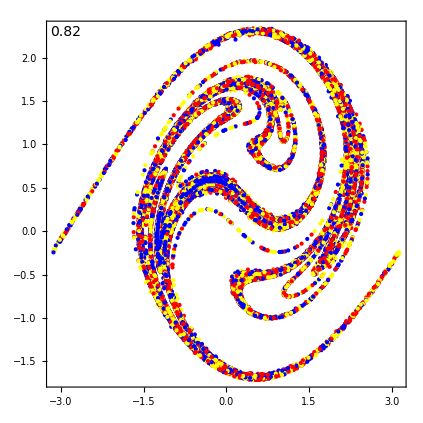

```mathematica
(* =====================================*)
(*Soluciones para cada conjunto de condiciones iniciales (ECUACIÓN ADIMENSIONAL)*)
(* =====================================*)
sols=Table[Module[{x0=cond[[1]],v0=cond[[2]]},NDSolve[{x''[t]+δ x'[t]+κ Sin[x[t]]-L Cos[x[t]-t]==0,x[0]==x0,x'[0]==v0},x,{t,0,tf},Method->{"StiffnessSwitching"},MaxSteps->Infinity]],{cond,CI}];

(* =====================================*)
(*Envolver ángulo a[-Pi,Pi) π/3*)
(* =====================================*)
α=0;
wrap[θ_]:=Mod[θ-α+π,2 π]-π+α

(* =====================================*)
(*Sección de Poincaré estroboscópica:muestreo cada T=2Pi (en t*)
(* =====================================*)
PE=Table[Table[{wrap[x[T*n]],x'[T*n]}/. sols[[i,1]],{n,500,Floor[tf/T]}],{i,1,Length[sols]}];
(*Gráfico estroboscópico*)
ListPlot[PE,PlotStyle->{{Yellow,PointSize[Tiny]},{Blue,PointSize[Tiny]},{Red,PointSize[Tiny]}},Frame->True,Axes->{False,False},AspectRatio->1,FrameLabel->{Style["",14],Style["",14]},LabelStyle->Directive[14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotRange->Full,PlotLegends->{Placed[Style[""<>ToString[κ],14],{Left,Top}],Placed[Style["",14],{0.94,Top}]}]
```

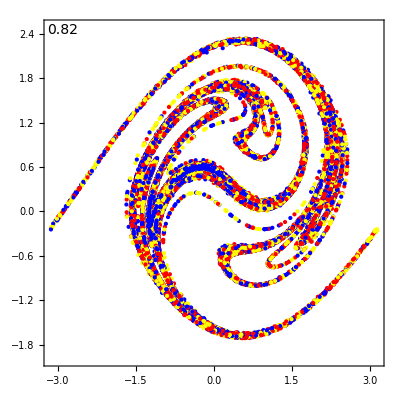

```mathematica
PE=Table[Table[{wrap[x[T*n]],x'[T*n]}/. sols[[i,1]],{n,500,Floor[tf/T]}],{i,1,Length[sols]}];
(*Gráfico estroboscópico*)
ListPlot[PE,PlotStyle->{{Yellow,PointSize[Tiny]},{Blue,PointSize[Tiny]},{Red,PointSize[Tiny]}},Frame->True,Axes->{False,False},AspectRatio->1,FrameLabel->{Style["",14],Style["",14]},LabelStyle->Directive[14],FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},PlotRange->{{-π,π},{-2,2.5}},PlotLegends->{Placed[Style[""<>ToString[κ],14],{Left,Top}],Placed[Style["",14],{0.94,Top}]}]
```